```mathematica
(* Common *)
On[Assert]
comment[c_][val_]:=(Print[c]; val);
Second[xs_]:=xs[[2]];
atNotebook[path_]:=FileNameJoin[{NotebookDirectory[],path}];
$AssertFunction=Print["ASSERTION FAILED: "<>ToString[##]]&;
inGroupsOf[n_][lst_]:=Partition[lst,n,n,{1,1},{}];

sanityCheck[]:=
Map[Block[{h=#},
Print["Testing "<>ToString[h]];
Assert[m0[h]≥0,"Negative mass"]; (* Non-negative mass *)
Assert[Γ0[h]≥0,"Negative width"]; (* Non-negative width *)
(*Assert[Sum[dec[[2]],{dec,decays[h]}]==1.,"Incomplete branching ratios for "<>ToString[h]];*)
Assert[2isoSpin[h]∈Integers,"Isospin is not half-integer for "<>ToString[h]]; (* Half-integer isospin *)
Assert[idMask[h]≠0,"Particle without mask is in Pythia"];(*Pythia particles must have id mask*)
Map[Module[{j1,j2,jOut,lChan,inRange,outRange,mmin},
j1=j@#[[1,1]];j2=j@#[[1,2]];jOut=j@h;lChan=#[[3]];
inRange=Range[Abs[j1-j2],Abs[j1+j2]];
outRange=Range[Abs[jOut-lChan],Abs[jOut+lChan]];
Assert[IntersectingQ[inRange,outRange],"Angular momenta inaccessible for "<>ToString[h]<>"-->"<>ToString[#[[1]]]]; (* Must be possible to conserve angular momentum *)

mmin=Sum[minMass@out,{out,#[[1]]}];
Assert[mmin≤ m0@h,"Minimum mass of decay products is higher than particle mass for "<>ToString[h]<>"-->"<>ToString[#[[1]]]]; (* Particles cannot decay to products with higher rest mass *)
]&,decays[h]];
True
]&,pythiaEntries];

pythiaEntries={
N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,
D1232,D1600,D1620,D1700,D1905,D1910,D1920,D1950,
L1405,L1520,L1600,L1670,L1690,L1690,L1800,L1810,L1820,L1830,L1890,L2100,L2110,
S1385,S1660,S1670,S1750,S1775,S1915,S1940,S2030,
X1530,X1820(*,
rho,omega,f0980,Kstar,phi,K0star,a0980,f01370,K11270,a11260,
f1,f11510,K21430,a21320,f21270,f21525,K11400,b11235,h11170,h11380,Kstar1680,rho1465*)
};


(* Kinematic and helper functions *)
ClearAll[BR]; ClearAll[massDecayBound];ClearAll[BRsum];
fitRegge[s_,z_,y1_,y2_]:=z+0.308Log[s/28.998]^2+y1(1./s)^0.458-y2(1./s)^0.545;
fitHERA[p_,a_,b_,n_,c_,d_]:=a+b p^n+c Log[p]^2+d Log[p];
breitWigner[Γ0_Real,dm_Real]:=Γ0/(dm^2+0.25Γ0^2)
getDecay[hIn_,hOuts_]:=SelectFirst[decays[hIn],#[[1]]==hOuts&];
BRsum[h_]:=BRsum[h]=Sum[dec[[2]],{dec,decays[h]}];
BR[hIn_,hOuts_]:=Block[{dec=getDecay[hIn,hOuts]},If[MissingQ[dec],0,dec[[2]]]]/BRsum[hIn];
isMeson[pi]=True;isMeson[pipi]=True;isMeson[eta]=True;isMeson[Ka]=True;
isMeson[h_]:=MemberQ[Ms,h];
decayAngularMomentum[hIn_,hOuts_]:=getDecay[hIn,hOuts][[3]];
decayProducts[particle_]:=First/@decays[particle];
minMass[particle_]:=
If[Γ0[particle]==0.,m0[particle],
Min[Table[Sum[minMass[product],{product,products}],{products,decayProducts[particle]}]]
];

massDecayBound[particle_]:=massDecayBound[particle]=
Min[(Total[minMass/@First[#]]&) /@ decays[particle]];

pCMS[eCM_,mA_,mB_]:=If[eCM≤mA+mB,0,1/(2.eCM)*Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]];
pLab[mA_,mB_,eCM_]:=If[eCM≤mA+mB,0,Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]/(2mB)];
pLabInv[mA_,mB_,pLab_]:=Sqrt[mA^2+mB^2+2mB Sqrt[mA^2+pLab^2]];

psSize[mDistribution_][eCM_,{hA_,hB_},lFac_:0]:=Module[{m0A,m0B},
m0A=m0[hA];m0B=m0[hB];
If[Γ0[hA]==0.&&Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@(pCMS[eCM,m0A,m0B]^lFac)]
];
If[Γ0[hA]==0.,
If[eCM<m0A+massDecayBound@hB,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]^lFac mDistribution[hB,mB],{mB,massDecayBound[hB],eCM-m0A}, PrecisionGoal->3,AccuracyGoal->10]
]];
If[Γ0[hB]==0.,
If[eCM<m0B+massDecayBound@hA,Return[0],
Return@NIntegrate[pCMS[eCM,mA,m0B]^lFac mDistribution[hA,mA],{mA,massDecayBound[hA],eCM-m0B}, PrecisionGoal->3,AccuracyGoal->10]
]];
If[eCM≤massDecayBound@hA+massDecayBound@hB,Return[0.]];
NIntegrate[pCMS[eCM,mA,mB]^lFac mDistribution[hA,mA]mDistribution[hB,mB],{mA,massDecayBound[hA],eCM-massDecayBound[hB]},{mB,massDecayBound[hB],eCM-mA}, PrecisionGoal->3,AccuracyGoal->10]
];

ClearAll[a0];
a0[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a0: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ0[particle],m0[particle]-m]/(2Pi)
];
p0Mean=psSize[a0];
ClearAll[p0MeanCh];
p0MeanCh[m0_,{hA_,hB_},lFac_]:=p0MeanCh[m0,{hA,hB},lFac]=p0Mean[m0,{hA,hB},lFac];

ClearAll[Γ];
Γ[hIn_,hOuts_,m_Real]:= Module[{br,p0,p0res,p01,p0res1,lChan},
If[m≤Sum[minMass[h],{h,hOuts}],Return[0]];
br=BR[hIn,hOuts];
If[br==0,Return[0]];
lChan=decayAngularMomentum[hIn,hOuts];

p01=p0Mean[m,hOuts,2lChan+1];
p0res1= p0MeanCh[m0[hIn],hOuts,2lChan+1];
p0=p0Mean[m,hOuts,2lChan]; 
p0res=p0MeanCh[m0[hIn],hOuts,2lChan];

Assert[p0res>0];Assert[p0res1>0];
Γ0[hIn] br* m0[hIn]/m * (p01/p0res1) * 1.2/(1. + 0.2(p0/p0res))
];
Γ[h_,m_]:=Sum[Γ[h,decs,m],{decs,decayProducts[h]}];


(* Define the mass distribution function and <p> *)
ClearAll[aN]; ClearAll[a];
aN[particle_]:=comment["Calculating aN for "<>ToString[particle],
aN[particle]=Re@NIntegrate[breitWigner[Γ[particle,m],m0[particle]-m],{m,massDecayBound[particle],Infinity}]
];

a[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
If[m≤0,0,breitWigner[Γ[particle,m],m0[particle]-m]/aN[particle]]
];
a[particle_,outs_,m_Real]:=
If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
If[m≤0,0,Γ[particle,outs,m]/((m-m0@particle)^2+0.25Γ[particle,m]^2)/aN[particle]]
];
pMean=psSize[a];

strangeFactor[h_]:=1.-0.4*strangeness[h]/If[isMeson[h],2.,3.];
```

```mathematica
sanityCheck[]
```

Testing N1440

Testing N1520

Testing N1535

Testing N1650

Testing N1675

Testing N1680

Testing N1700

Testing N1710

Testing N1720

Testing D1232

Testing D1600

Testing D1620

Testing D1700

Testing D1905

Testing D1910

Testing D1920

Testing D1950

Testing L1405

Testing L1520

Testing L1600

Testing L1670

Testing L1690

Testing L1690

Testing L1800

Testing L1810

Testing L1820

Testing L1830

Testing L1890

Testing L2100

Testing L2110

Testing S1385

Testing S1660

Testing S1670

Testing S1750

Testing S1775

Testing S1915

Testing S1940

Testing S2030

Testing X1530

Testing X1820

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Γ[D1232, 2.]
```

1.00531

```mathematica
Γ[D1232,{N938,pi},2.]
```

1.00531

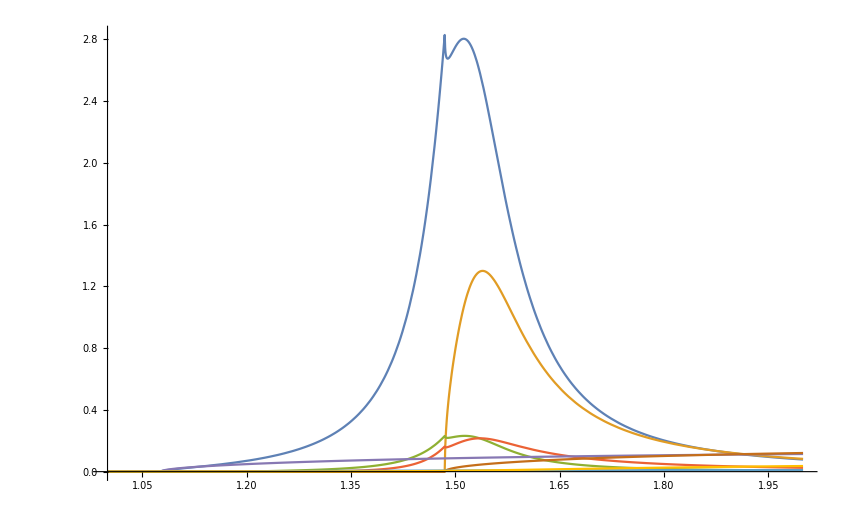

```mathematica
Plot[Evaluate@Flatten[{
Table[a[N1535,outs,m],{outs,decayProducts[N1535]}],
Table[Γ[N1535,outs,m],{outs,decayProducts[N1535]}]
},2],{m,1.,2.},PlotRange->All]
```

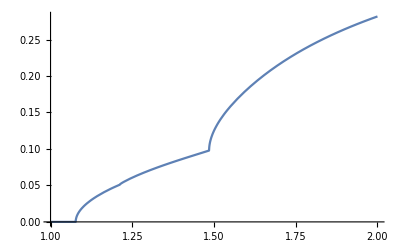

```mathematica
Plot[Γ[N1535,m],{m,1.,2.}]
```

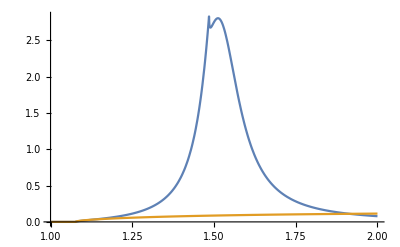

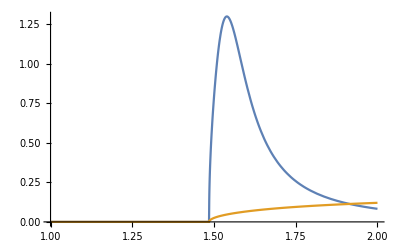

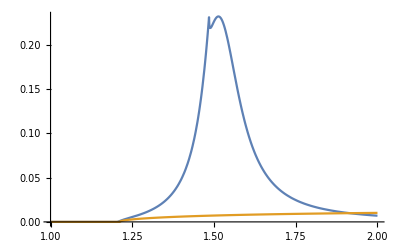

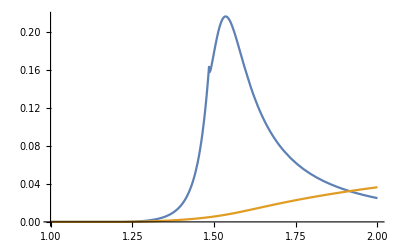

{Null,Null,Null,Null}

```mathematica
Table[Print@Plot[{a[N1535,outs,m],Γ[N1535,outs,m]},{m,1.,2.},PlotRange->All],{outs,decayProducts@N1535}]
```

```mathematica
minMass@omega
```

```mathematica
Γ[omega,{pi,pi},0.15]
```

7.50439×10^-8

```mathematica
Plot[Γ
```

```mathematica
minMass[D1232]
```

1.07757

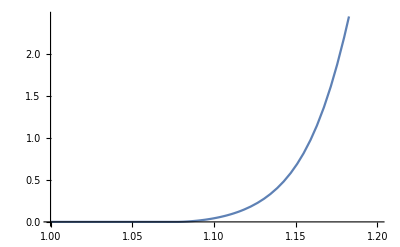

```mathematica
Plot[a[D1232,m],{m,1.,1.2}]
```

```mathematica
minMass[rho]
```

0.27914

```mathematica
Table[a[rho,m],{m,0.,1.,0.01}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.95112×10^-6,0.000414158,0.00113853,0.00211871,0.00334326,0.00481584,0.00654828,0.00855842,0.0108693,0.0135089,0.0165107,0.0199138,0.0237638,0.0281138,0.033025,0.0385691,0.0448291,0.0519017,0.0599003,0.0689573,0.0792291,0.0908998,0.104188,0.119353,0.136707,0.156622,0.179548,0.20603,0.236732,0.272465,0.314225,0.363239,0.421025,0.489461,0.570875,0.66814,0.784777,0.925039,1.09392,1.29703,1.54006,1.82772,2.16159,2.53666,2.93682,3.331,3.67371,3.91437,4.01466,3.96458,3.78554,3.51864,3.20784,2.88837,2.58306,2.30393,2.05545,1.83767,1.64836,1.48438,1.34241,1.2193,1.11225,1.01883,0.936992,0.864993,0.801382,0.744945,0.694665,0.64969,0.609306,0.572909,0.539989}

```mathematica
pts=Monitor[
Table[
Print@ListLinePlot[Table[{mm,a[h,mm]},{mm,1.,2.8,0.01}],PlotRange->All,PlotLegends->ToString[h]],{h,Xs}],
{ProgressIndicator[mm,{0.,4.}],h}
];
```

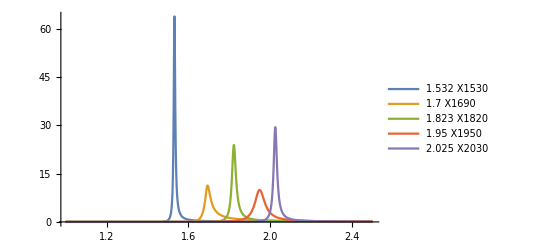

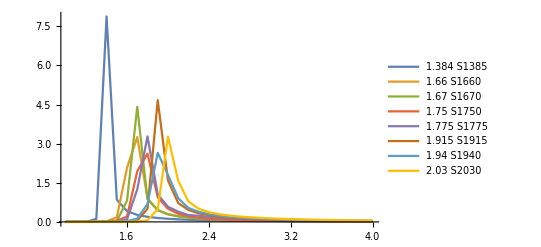

```mathematica
pts=Monitor[
Table[{h m0[h],Table[{mm,a[h,mm]},{mm,1.,2.5,0.001}]},{h,Xs}],
{ProgressIndicator[mm,{0.,4.}],h}
];
ListLinePlot[Second/@pts,PlotRange->All,PlotLegends->First/@pts]
```

```mathematica
Monitor[
Plot[Evaluate@Table[Γ[h,eee],{h,Ss},{eee,mMin[h],mMax[h]}],PlotRange->All,PlotLegends->ToString/@Ls],
{ProgressIndicator[eee,{1,5}],h}
]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{{0.00618335,0.4713},{0.00867181,0.47684,0.793386},{0.00768386,0.506616},{0.0212579,0.404983},{0.0067059,0.904823,1.32349},{0.0189563,0.81517,1.02221},{0.0227568,0.774678,1.22391,1.39108},{0.00819949,1.19142,1.61797,1.73239}},PlotRange→All,PlotLegends→ToString/@Ls]

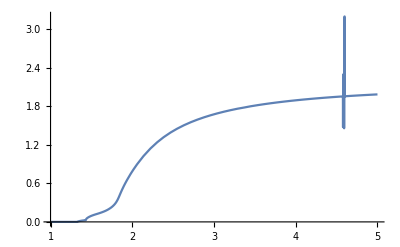

```mathematica
Monitor[
Plot[Γ[L1800,mm],{mm,1,5},PlotRange->All],
ProgressIndicator[mm,{1,5}]
]
```

```mathematica
Plot[Evaluate@Table[a[d,m],{d,Ds}],{m,1,5},PlotLegends->Ds,PlotRange->All]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.72396}. NIntegrate obtained 7.22642 and 0.0000225444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.73709}. NIntegrate obtained 6.50815 and 0.000151479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.92073}. NIntegrate obtained 6.67456 and 0.000034439 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
pts=Monitor[
Table[{outs,Table[Γ[N1535,outs,m],{m,1.,3.99,0.05}]},{outs,decayProducts[N1535]}],
{d,ProgressIndicator[m,{1.,5.}]}
];
```

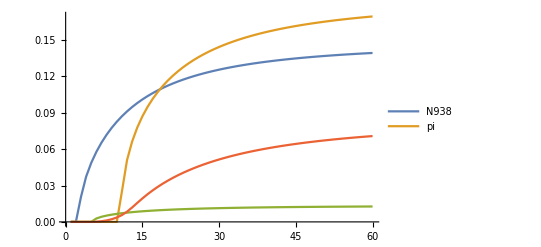

```mathematica
ListLinePlot[Second/@pts,PlotLegends->First/@pts]
```

```mathematica
(* Write all kinds of outputs to different files *)
Monitor[
Table[
Module[{dir,files,gammaTotal,pts},
dir=atNotebook[ToString[h]];
If[DirectoryQ[dir],DeleteDirectory[dir,DeleteContents->True]];
CreateDirectory[dir];

files=Table[ToString@h<>"/br_"<>StringRiffle[ToString/@outs,"_"],{outs,decayProducts[h]}];

pts=Table[Table[Γ[h,outs,m],{m,mMin[h],mMax[h],0.01}],{outs,decayProducts[h]}];
gammaTotal=Total[pts];
pts = pts/Table[gammaTotal/.{0.->Infinity},Length[pts]];

writeInterpolationData[ToString[h]<>"/Gamma",gammaTotal];
Table[writeInterpolationData[p[[1]],p[[2]]],{p,Transpose[{files,pts}]}];
]
,{h,Join[Ns,Ds]}],
{h,Catch@ProgressIndicator[m,{mMin[h],mMax[h]}]}]
```

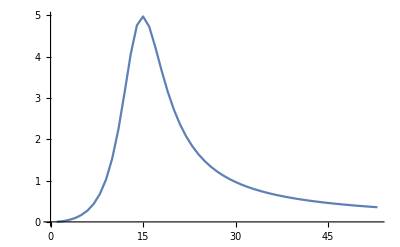

```mathematica
ListLinePlot[Table[a[D1232,m],{m,mMin[D1232],mMax[D1232],0.01}]]
```

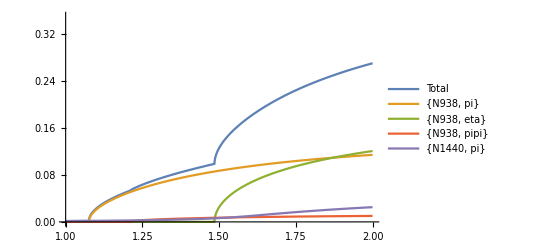

```mathematica
Block[{h=N1535},
Module[{},
Plot[Evaluate@Flatten@{Γ[h,m],Table[Γ[h,outs,m],{outs,decayProducts[h]}]},{m,1.,2.},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]},PlotRange->{0.,0.35}]
]
]
```

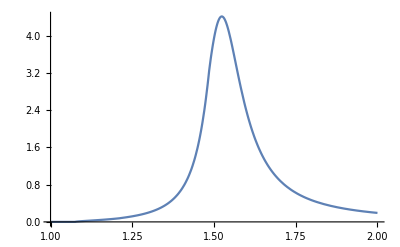

```mathematica
Plot[a[N1535,m],{m,1.,2.},PlotRange->All]
```

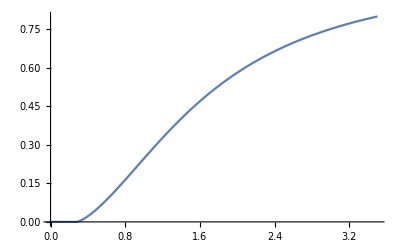

```mathematica
Plot[Γ[rho,m],{m,0.,3.5}]
```

```mathematica
pts=Block[{h=N1535},
Table[Table[Γ[h,outs,m],{m,mMin[h]+.1,mMax[h],0.1}],{outs,decayProducts[h]}]
]
```

```mathematica
pts/Table[Total[pts],Length[pts]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Length@pts[[4]]
```

40

```mathematica
{{a1,b1,c1,d1},{a2,b2,c2,d2}}/{x,y,z,w}
```

Thread::tdlen: Objects of unequal length in {{a1,b1,c1,d1},{a2,b2,c2,d2}} {1/x,1/y,1/z,1/w} cannot be combined.

{{a1,b1,c1,d1},{a2,b2,c2,d2}} {1/x,1/y,1/z,1/w}

```mathematica
Total@pts
```

{0.0210838,0.0487912,0.0701582,0.0857999,0.124977,0.181073,0.216145,0.24279,0.264022,0.281452,0.296051,0.308458,0.319122,0.328376,0.336467,0.343592,0.349902,0.355522,0.36055,0.365069,0.369146,0.372839,0.376194,0.379253,0.38205,0.384613,0.38697,0.389141,0.391146,0.393002,0.394723,0.396322,0.39781,0.399198,0.400494,0.401707,0.402843,0.403909,0.40491,0.405852}

```mathematica
Directory
```